# LIRE: Lissajous-figure Reconstruction for nonlinear polarization tomography of bichromatic fields - Usage and examples

© Emilio Pisanty 2019. Licensed under GPL and CC-BY-SA.

### Readme

LIRE is a Mathematica package for reconstructing the polarization Lissajous figures of bichromatic ω:2ω light-beam combinations, as described in the paper

 • Knotting fractional-order knots with the polarization state of light. E. Pisanty et al. Nature Photonics, in press (2019), arXiv:1808.05193.

This file provides documentation on the usage of the different functions of the package as well as some benchmarking.

## Usage and Examples

### Loading the package

To load this package, please ensure that a copy of the package file is on the same location as your usage notebook, and run the command

```mathematica
Needs["LIRE`",FileNameJoin[{NotebookDirectory[],"LIRE.m"}]]
```

The package can also be called from some  separate directory, by suitably modifying the second argument above.

For longer-term usage, it is more convenient to fully install the package, which can be done by placing a copy of LIRE.m (or a soft link to that file) in your Mathematica applications directory, $UserBaseDirectory/Applications/. In that case, the package can simply be called via

```mathematica
Needs["LIRE`"]
```

or even more simply

```mathematica
<<LIRE`
```

To print the version of the package in use, use the command

```mathematica
$LIREversion
```

LIRE v1.0.0, Sun 17 Mar 2019 01:18:13

There are also commands to get the $LIREtimestamp directly, as well as the git $LIREcommit hash and message.

```mathematica
Quit
```

### Usage messages of the different package functions

```mathematica
?UnitE
```

UnitE[1] and UnitE[-1] return, respectively, 1/(√2){1,ⅈ} and 1/(√2){1,-ⅈ}.

```mathematica
?EnsureRightCircularFundamental
```

EnsureRightCircularFundamental[{E1p,E1m,E2p,E2m}] ensures that the fundamental has right-circular polarization (i.e. |E1p|>|E1m|) by swapping the input to {E1m*,E1p*,E2m*,E2p*} if necessary.

```mathematica
?PhaseNormalization
```

PhaseNormalization[{E1p,E1m,E2p,E2m}] Normalizes the field phases so that E1p is real and positive, by multiplying by an appropriate factor of ⅇ^(-ⅈ ϕ) on E1 and ⅇ^(-2 ⅈ ϕ) on E2.

```mathematica
?NLPTOutcomes
```

NLPTOutcomes[{ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m}] Calculates the Nonlinear Polarization Tomography outcome functions I_n, as defined in the paper, with the normalization set so that the ℓ>0 components of the paper are given by I_ℓ^paper(θ)=Re(2I_ℓⅇ^(ⅈ ℓ θ)).

NLPTOutcomes[{E1p,E1m,E2p,E2m}] Uses explicit complex amplitudes.

```mathematica
?ReconstructionMimimizationTarget
```

ReconstructionMimimizationTarget[{I0,I1,I2,I3,I4}][ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m] calculates the reconstruction target ∑_(n=0)^4 , i.e. the sum of squares of the nonlinear-polarimetry Fourier coefficients in difference between the given I_n and those reconstructed from the given complex fields.

```mathematica
?ReconstructBicircularFieldList
```

ReconstructBicircularFieldList[{I0,I1,I2,I3,I4}] calculates a list of candidate reconstructed fields (each an Association of the form <|"Fields"→{E_(1+),E_(1-),E_(2+),E_(2-)},"Outcomes"→{I_(0, rec),I_(1, rec),I_(2, rec),I_(3, rec),I_(4, rec)},"√Residual"→r,"Residual"→r^2|>), obtained by minimizing ReconstructionMimimizationTarget over a list of random initial seeds pulled from a box of side 1.

ReconstructBicircularFieldList[{I0,I1,I2,I3,I4},Erange] uses a box of side Erange (which can be a single number, or a list of eight real numbers to be used as the sizes of the boxes for {ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m}) for the initial seeds of the minimization.

ReconstructBicircularFieldList[{I0,I1,I2,I3,I4},Erange,iterations] uses the specified number of iterations.

```mathematica
?ReconstructBicircularField
```

ReconstructBicircularField[{I0,I1,I2,I3,I4}] returns the first element of the corresponding ReconstructBicircularFieldList, using the specified (or default) SortingFunction.

ReconstructBicircularField[{I0,I1,I2,I3,I4},Erange] returns the first element of the corresponding ReconstructBicircularFieldList, using the specified (or default) SortingFunction.

ReconstructBicircularField[{I0,I1,I2,I3,I4},Erange,iterations] returns the first element of the corresponding ReconstructBicircularFieldList, using the specified (or default) SortingFunction.

### The formal expression of the NLPTOutcomes

```mathematica
NLPTOutcomes[{ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m}]
```

{ImE1m^4/8+(ImE1m^2 ImE1p^2)/2+ImE1p^4/8+ImE2m^2/4+ImE2p^2/4+(ImE1m^2 ReE1m^2)/4+(ImE1p^2 ReE1m^2)/2+ReE1m^4/8+(ImE1m^2 ReE1p^2)/2+(ImE1p^2 ReE1p^2)/4+(ReE1m^2 ReE1p^2)/2+ReE1p^4/8+ReE2m^2/4+ReE2p^2/4,-(ⅈ ImE1m^2 ImE2m)/(4 √2)+(ⅈ ImE1m ImE1p ImE2m)/(2 √2)-(ⅈ ImE1m ImE1p ImE2p)/(2 √2)+(ⅈ ImE1p^2 ImE2p)/(4 √2)+(ImE1m ImE2m ReE1m)/(2 √2)+(ImE1p ImE2m ReE1m)/(2 √2)+(ImE1p ImE2p ReE1m)/(2 √2)+(ⅈ ImE2m ReE1m^2)/(4 √2)+(ImE1m ImE2m ReE1p)/(2 √2)+(ImE1m ImE2p ReE1p)/(2 √2)+(ImE1p ImE2p ReE1p)/(2 √2)-(ⅈ ImE2m ReE1m ReE1p)/(2 √2)+(ⅈ ImE2p ReE1m ReE1p)/(2 √2)-(ⅈ ImE2p ReE1p^2)/(4 √2)-(ImE1m^2 ReE2m)/(4 √2)-(ImE1m ImE1p ReE2m)/(2 √2)-(ⅈ ImE1m ReE1m ReE2m)/(2 √2)+(ⅈ ImE1p ReE1m ReE2m)/(2 √2)+(ReE1m^2 ReE2m)/(4 √2)+(ⅈ ImE1m ReE1p ReE2m)/(2 √2)+(ReE1m ReE1p ReE2m)/(2 √2)-(ImE1m ImE1p ReE2p)/(2 √2)-(ImE1p^2 ReE2p)/(4 √2)-(ⅈ ImE1p ReE1m ReE2p)/(2 √2)-(ⅈ ImE1m ReE1p ReE2p)/(2 √2)+(ⅈ ImE1p ReE1p ReE2p)/(2 √2)+(ReE1m ReE1p ReE2p)/(2 √2)+(ReE1p^2 ReE2p)/(4 √2),(ImE1m^3 ImE1p)/4+(ImE1m ImE1p^3)/4+(ImE2m ImE2p)/4+1/4 ⅈ ImE1m^2 ImE1p ReE1m+1/4 ⅈ ImE1p^3 ReE1m+1/4 ImE1m ImE1p ReE1m^2+1/4 ⅈ ImE1p ReE1m^3-1/4 ⅈ ImE1m^3 ReE1p-1/4 ⅈ ImE1m ImE1p^2 ReE1p+1/4 ImE1m^2 ReE1m ReE1p+1/4 ImE1p^2 ReE1m ReE1p-1/4 ⅈ ImE1m ReE1m^2 ReE1p+(ReE1m^3 ReE1p)/4+1/4 ImE1m ImE1p ReE1p^2+1/4 ⅈ ImE1p ReE1m ReE1p^2-1/4 ⅈ ImE1m ReE1p^3+(ReE1m ReE1p^3)/4+(ⅈ ImE2p ReE2m)/4-(ⅈ ImE2m ReE2p)/4+(ReE2m ReE2p)/4,(ⅈ ImE1p^2 ImE2m)/(4 √2)-(ⅈ ImE1m^2 ImE2p)/(4 √2)+(ImE1m ImE2p ReE1m)/(2 √2)+(ⅈ ImE2p ReE1m^2)/(4 √2)+(ImE1p ImE2m ReE1p)/(2 √2)-(ⅈ ImE2m ReE1p^2)/(4 √2)-(ImE1p^2 ReE2m)/(4 √2)+(ⅈ ImE1p ReE1p ReE2m)/(2 √2)+(ReE1p^2 ReE2m)/(4 √2)-(ImE1m^2 ReE2p)/(4 √2)-(ⅈ ImE1m ReE1m ReE2p)/(2 √2)+(ReE1m^2 ReE2p)/(4 √2),(ImE1m^2 ImE1p^2)/8+1/4 ⅈ ImE1m ImE1p^2 ReE1m-(ImE1p^2 ReE1m^2)/8-1/4 ⅈ ImE1m^2 ImE1p ReE1p+1/2 ImE1m ImE1p ReE1m ReE1p+1/4 ⅈ ImE1p ReE1m^2 ReE1p-(ImE1m^2 ReE1p^2)/8-1/4 ⅈ ImE1m ReE1m ReE1p^2+(ReE1m^2 ReE1p^2)/8}

### Single-run reconstruction of a randomly-generated field

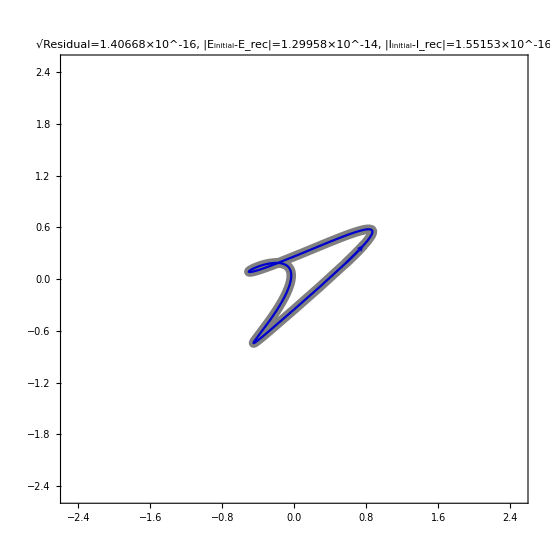

```mathematica
Block[{initialFields,initialValues,solution},

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];

initialValues=NLPTOutcomes[initialFields];

solution=ReconstructBicircularField[initialValues,1,15];


ParametricPlot[{
Evaluate[Tooltip[
(*1.03×*)Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->initialFields
]
,"Initial fields"]],
Evaluate[Tooltip[
Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->solution["Fields"]
]
,"Reconstruction"]]
},{ωt,0,2π}
,PlotStyle->{Directive[Thickness[0.0125],Arrowheads[0.075],GrayLevel[0.5]],Directive[Darker[Blue,0.2]]}
,PlotRange->2.5{{-1,1},{-1,1}}
,PlotPoints->25
,MaxRecursion->2
,Frame->True
,ImageSize->550
,Method->{"AxesInFront"->False}
,AxesStyle->GrayLevel[0.85]
,PlotLabel->Row[{
"√Residual=",solution["√Residual"],",  ",
"|E_initial-E_rec|=",Norm[initialFields-solution["Fields"]],",  ",
"|I_initial-I_rec|=",Norm[initialValues-NLPTOutcomes[solution["Fields"]]]
}]
]/.{Line[pts_]:>{{Line[pts],Arrow[pts⟦-5;;-1⟧]}}}

]
```

I.e. the blue curve lies completely on top of the gray curve, meaning that (unless the convergence failed, and returned a sub-optimal local minimum, which it can do!) the reconstruction is essentially perfect to within machine accuracy.

### Array of reconstructions over multiple randomly-generated initial fields

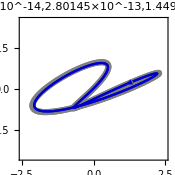
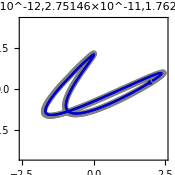
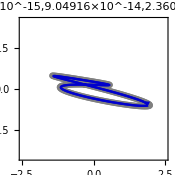
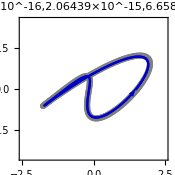
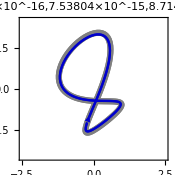
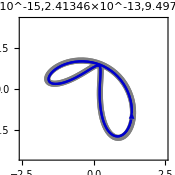
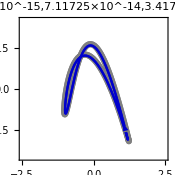
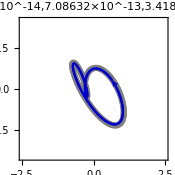

```mathematica
Block[{initialFields,initialValues,solution},

Table[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];
solution=ReconstructBicircularField[initialValues,1,10];

ParametricPlot[{
Evaluate[Tooltip[
1.03×Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->initialFields
]
,"Initial fields"]],
Evaluate[Tooltip[
Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->solution["Fields"]
]
,"Reconstruction"]]
},{ωt,0,2π}
,PlotStyle->{Directive[Thickness[0.025],Arrowheads[0.15],GrayLevel[0.5]],Directive[Arrowheads[0.1],Darker[Blue,0.2]]}
,PlotRange->2.5{{-1,1},{-1,1}}
,PlotPoints->25
,MaxRecursion->2
,Frame->True
,ImageSize->175
,Method->{"AxesInFront"->False}
,AxesStyle->GrayLevel[0.85]
,PlotLabel->Style[{
solution["√Residual"],
Norm[initialFields-solution["Fields"]],
Norm[initialValues-NLPTOutcomes[solution["Fields"]]]
},FontSize->7]
]/.{Line[pts_]:>{{Line[pts],Arrow[pts]}}}

,{18}]

]
```

### Array of reconstructions over multiple randomly-generated initial fields - with a low iteration number, leading to more errors

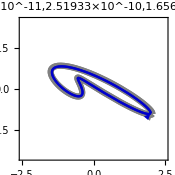
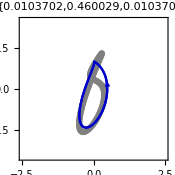
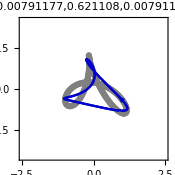
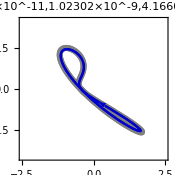
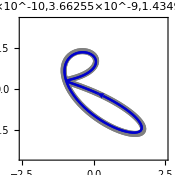
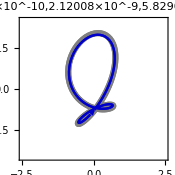
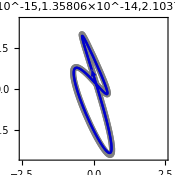
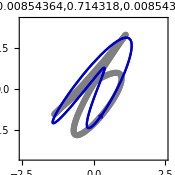

```mathematica
Block[{initialFields,initialValues,solution},

Table[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];
solution=ReconstructBicircularField[initialValues,1,1];

ParametricPlot[{
Evaluate[Tooltip[
1.03×Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->initialFields
]
,"Initial fields"]],
Evaluate[Tooltip[
Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->solution["Fields"]
]
,"Reconstruction"]]
},{ωt,0,2π}
,PlotStyle->{Directive[Thickness[0.025],Arrowheads[0.15],GrayLevel[0.5]],Directive[Arrowheads[0.1],Darker[Blue,0.2]]}
,PlotRange->2.5{{-1,1},{-1,1}}
,PlotPoints->25
,MaxRecursion->2
,Frame->True
,ImageSize->175
,Method->{"AxesInFront"->False}
,AxesStyle->GrayLevel[0.85]
,PlotLabel->Style[{
solution["√Residual"],
Norm[initialFields-solution["Fields"]],
Norm[initialValues-NLPTOutcomes[solution["Fields"]]]
},FontSize->7]
]/.{Line[pts_]:>{{Line[pts],Arrow[pts]}}}

,{18}]

]
```

### Convergence properties with respect to the iterations number

#### Distribution of error sizes over the iterations for fixed (random) single initial field

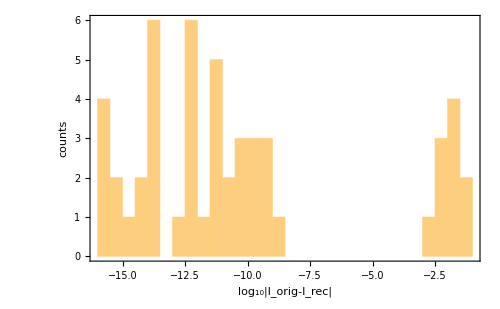

```mathematica
Block[{initialFields,initialValues,solution},
Histogram[
Table[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];

solution=ReconstructBicircularField[initialValues,1,3];

Log10[solution["√Residual"]]

,{50}]
,{0.5}
,Frame->True
,FrameLabel->{"log_10|I_orig-I_rec|","counts"}
,ImageSize->500
]

]
```

This implies that the error is either quite large (with |I_orig-I_rec| of the order of a few percent) or it is very small, with the √residual rather smaller than 10^-10. 

That then implies that it is relatively simple to divide the guesses into successes and failures, by setting up a suitable cut point at some point in that large gap - below we set it at  log_10|I_orig-I_rec|=-7.

#### Convergence testing

The code below runs the reconstruction algorithm at increasing iteration numbers, and then counts the successes and failures at each number of iterations.

Sun 17 Mar 2019 03:45:25

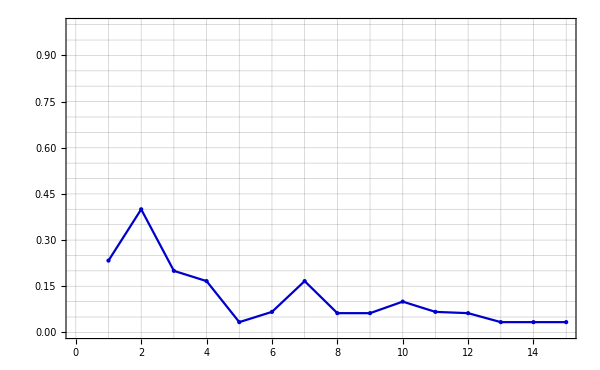
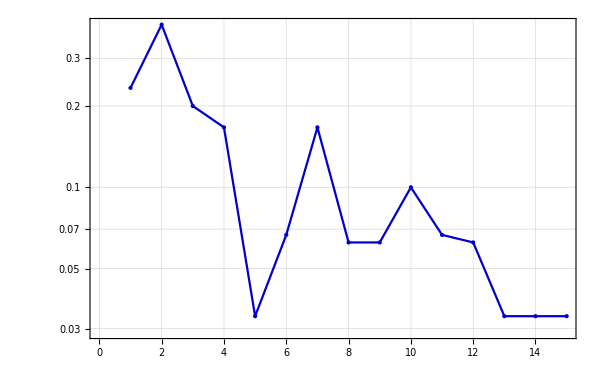

Sun 17 Mar 2019 03:47:46

```mathematica
DateString[]
Block[{initialFields,initialValues,solution,runsPerIterations,maxIterations},
runsPerIterations=30(*1000*);
maxIterations=15(*24*);
convergenceTestData=Table[
{iterations,N[Length[#[True]]/(Length[#[False]]+Length[#[True]])]}&[
GroupBy[
ParallelTable[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];

solution=Quiet[
ReconstructBicircularField[initialValues,1,iterations]
,{FindMinimum::cvmit,FindMinimum::sszero}];

Log10[solution["√Residual"]]

,{runsPerIterations}]
,#>-7&
]
]
,{iterations,1,maxIterations}
];
Row[{
ListPlot[
convergenceTestData
,PlotStyle->Directive[PointSize[Large],Darker[Blue,0.2]]
,Frame->True
,GridLines->All
,ImageSize->600
,PlotRange->{0,1}
]/.{Point[pts_]:>{Point[pts],Line[pts]}},
ListLogPlot[
convergenceTestData
,PlotStyle->Directive[PointSize[Large],Darker[Blue,0.2]]
,Frame->True
,GridLines->All
,ImageSize->600
]/.{Point[pts_]:>{Point[pts],Line[pts]}}
}]
]
DateString[]
```

The result is clearly exponential, which means that the error rate goes down exponentially with the iterations number (as would be expected). This then lets us fit the convergence data to a model, to quantify the failure rate per iteration.

#### Quantifying the failure rate

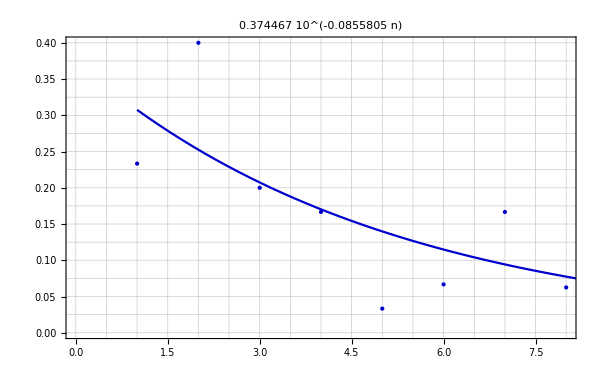

```mathematica
Block[{model},
model=NonlinearModelFit[convergenceTestData⟦1;;10⟧,A 10^(-n/R),{A,R},{n}];
Show[{
ListPlot[
convergenceTestData⟦1;;8(*10*)⟧
,PlotStyle->Directive[PointSize[Large],Darker[Blue,0.2]]
,Frame->True
,GridLines->All
,ImageSize->600
,PlotLabel->model[n]
],
Plot[
model[n]
,{n,1,10}
,PlotStyle->Directive[Darker[Blue,0.2]]
]
}]
]
```

i.e., we have

```mathematica
NonlinearModelFit[convergenceTestData⟦1;;10⟧,A 10^(-n/R),{A,R},{n}]["BestFitParameters"]
```

{A→0.374467,R→11.6849}

or, in other words, about a factor-of-ten decrease in the error rate for every additional R=11 iterations, with a failure rate of 3.7% at n=11 iterations.